# MA2330

## Chapter 6 : Orthogonality and Least Squares

At the start of the course we considered linear systems described by matrices A∈ℝ^(m×n) with m≤n: remember m is the number of equations and n is the number of unknowns.   When m=n we had a square system and had a unique solution x=A^-1 b to A x=b provided the columns of A were LI.  When m<n we had fewer equations than unknowns and we could write down all the solutions by identifying free variables from the RREF.

The topic of this chapter is the remaining case m>n when we have more equations than unknowns and the system A x=b is almost always inconsistent!  Since we can not solve the system we try to make the residual
	b-A x
as small as possible. To make it small we need to decide how to measure it.  We also need to set up some definitions and tools.

Think about trying to run a polynomial through some noisy data. I want the best polynomial (of some degree) that fits the data below.

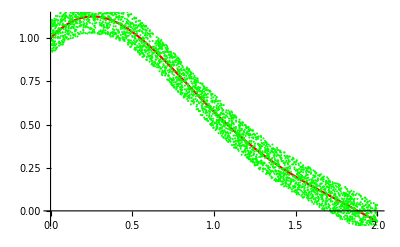

```mathematica
Clear[f,x]
f[x_]:= Sin[x]+Cos[x+ Sin[x]]
ϵ=0.1; SampleSize=3230;
AASData=Table[ x=RandomReal[{0,2}];{x, f[x]+ϵ RandomReal[{-1,1}]},{SampleSize}];
Show[
Plot[f[x],{x,0,2},PlotStyle->Red],
ListPlot[AASData, PlotStyle->Green]]
```

There is a built in fit command in Mathematica. We want to understand what they are doing.

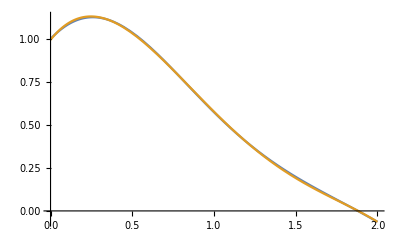

```mathematica
Plot[{f[x],p4[x]},{x, 0, 2}]
```

```mathematica
Clear[x]
p2[x_]=Fit[AASData,{1,x,x^2},x]
p3[x_]=Fit[AASData,{1,x,x^2,x^3},x]
p4[x_]=Fit[AASData,{1,x,x^2,x^3,x^4},x]
Fit[AASData,Table[x^i,{i,0,4}],x]
```

1.23135-0.558275 x-0.0676334 x^2

1.06928+0.439226 x-1.32499 x^2+0.421177 x^3

0.994721+1.19994 x-3.0436 x^2+1.76184 x^3-0.336156 x^4

0.994721+1.19994 x-3.0436 x^2+1.76184 x^3-0.336156 x^4

There is nothing special about Mathematica. Julia, Python, Matlab, …all have a linear fitting command. They all run similar algorithms.

Important property of transpose and inner product.
	u.(A v)=(Aᵀu).v

```mathematica
m=3;
{u,v}=RandomReal[{-1,1},{2,m}];
A=RandomReal[{-1,1},{m,m}];
u.(A.v)
(Aᵀ.u).v
```

0.359041

0.359041

### 6.1 Inner Product, Length and Orthogonality

Much of this is a review from calculus.

Definition: For u, v ∈ ℝ^n the inner product or dot product is  u.v=∑_(i=1)^n u_i v_i=uᵀv

```mathematica
Clear[v]
{6,7,5}.Array[v,3]
```

6 v[1]+7 v[2]+5 v[3]

Definition: For u∈ ℝ^n the length or norm of u is||u||=√(u.u)=√(∑_(i=1)^n u_i^2)

```mathematica
Clear[v]
Norm[Array[v,4]]
```

√(Abs[v[1]]^2+Abs[v[2]]^2+Abs[v[3]]^2+Abs[v[4]]^2)

Theorem 1: u.v=v.u;  (u+v).w=u.w+v.w; (c u).v=c u.v = u.(c v); u.u≥0; and u.u=0 iff u=0.

Definition: The distance between u and v in ℝ^n is dist(u,v)=||u-v||

This is just the distance formula!

Definition: The angle between u,v∈ℝ^n is defined by u.v=||u||||v||cos(θ). They are orthogonal if u.v=0.

Again straight from Calculus.

Theorem 2: Pythagorean
Vectors u,v∈ℝ^n are orthogonal iff ||u+v(||)^2=||u(||)^2+||v(||)^2

It really is just the Pythagorean theorem.

```mathematica
n=3;
u =RandomReal[{-1,1},n];
v=RandomReal[{-1,1},n];
v=v-(v.u)/(u.u) u;
Graphics3D[{ Thick,
{Red, Arrow[{{0,0,0},u}]},
{Blue, Arrow[{{0,0,0},v}]},
{Green,Arrow[{{0,0,0},u+v}]},
{LightPink, Arrow[{u,u+v}]},
{LightBlue, Arrow[{v,u+v}]}
}]
```

-Graphics3D-

Orthogonality extends to subspaces.

Definition: A subspace W⊂ℝ^n is orthogonal to a vector z∈ℝ^n if w.z=0 for all w∈W.

```mathematica
n=3;
u =Normalize[RandomReal[{-1,1},n]];
v=RandomReal[{-1,1},n];
v=Normalize[v-(v.u)u]; 
z=2RandomReal[{-1,1},n];
{zu,zv}={(z.u)u,(z.v)v};
zPerp=z-zu - zv;
Show[
ParametricPlot3D[u t + v s, {t, -1.5,1.5},{s,-1.5,1.5}],
Graphics3D[{ Thick,
{Red, Arrow[{{0,0,0},u}]},
{Blue, Arrow[{{0,0,0},v}]},
{Black, Arrow[{{0,0,0},z}]},
{Purple, Arrow[{{0,0,0},zu+zv,z}]}
}],
PlotRange->2{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

Definition: The orthogonal complement of a subspace W⊂ℝ^n is the set of all such z
	W^⊥={z: w.z=0 ∀w∈W}

This is a subspace.  We already know how to build it out of a basis for W.

Reminder Definition: The row space of a matrix A∈ℝ^(m×n) is the span of the rows of A and the column space is the span of the columns. The null space of A is the set of all solutions of A x=0.  Clearly
	row(A)⊂ℝ^n,  col(A)⊂ℝ^m, nul(A)⊂ℝ^n, and nul(Aᵀ)⊂ℝ^m

Theorem 3: 
	(row(A))^⊥ | = | nul(A)  
(col(A))^⊥ | = | nul(Aᵀ)

### 6.2 Orthogonal Sets

The motto is orthogonal sets are very useful.

Definition: A set of vectors For {u_1,u_2,…,u_p}in  ℝ^n is orthogonal if u_i.u_j=0 for i≠j.

Theorem 4: If S={u_1,u_2,…,u_p} is an orthogonal set of non-zero vectors the S is Linearly Independent (LI). As a result S is a basis for span(S).

Definition: An orthogonal basis for a subspace W⊂ℝ^n is a basis for W that is orthogonal.

There is a simple recipe for the coefficients y=c_1 u_1+c_2 u_2+…+c_p u_p if the us are orthogonal.

Theorem 5: If S={u_1,u_2,…,u_p} is an orthogonal basis for W⊂ℝ^n then for y∈W is the linear combination
	y=c_1 u_1+c_2 u_2+…+c_p u_p=∑_(i=1)^n c_i u_i
where 
	c_i=(y.u_i)/(u_i.u_i).

It would be even simpler if we normalized the basis to have u_i.u_i=1.

Definition: An orthonormal basis for a subspace W⊂ℝ^n is an orthogonal basis that is normalized.

If {u_1,u_2,…,u_p} is an orthogonal basis for W then  {u_1/(||u_1||),u_2/(||u_2||),…,u_p/(||u_p||)} is an orthogonal basis for W.

Theorem 6: An m×n matrix U has orthonormal columns iff Uᵀ U=I_n.

Theorem 7: If U∈ℝ^(n×n) has orthonormal columns and x,y∈ℝ^n then 
||U x||=||x||, (U x).(U y) = x.y, and (U x).(U y) = 0 iff x.y=0.

Definition: An orthogonal matrix is a square matrix with orthonormal columns.

Theorem:  If U∈ℝ^(n×n) is orthogonal then U^-1=Uᵀ.

If we think about it we already know how to build an orthogonal basis. Here is a computation for the column space of a Tall Skinny (TS) matrix A∈ℝ^(m×n) with m>n.

```mathematica
{m,n}={4,3};
A=RandomReal[{-1,1},{m,n}];
(* Fix the length of column 1 *)
u1=Normalize[A⟦All,1⟧];
(* Work on column 2 *)
u2=A⟦All,2⟧;
u2=u2 -(u1.u2) u1;
u2=Normalize[u2];
(* Work on column 3 *)
u3=A⟦All,3⟧;
u3=u3 -(u1.u3) u1;
u3=u3 -(u2.u3) u2;
u3=Normalize[u3];
(* Assemble a matrix U from the columns *)
U={u1,u2,u3}ᵀ;
MatrixForm[Chop[Uᵀ.U]]
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

This is called the Gram-Schmidt process and is a very common thing to do to a matrix because “Orthogonal basis are very useful!”  As we will see it is called the QR decomposition.

{{156,25},{156,25},{25,25}}

4.09817×10^-15

1.17092×10^-15

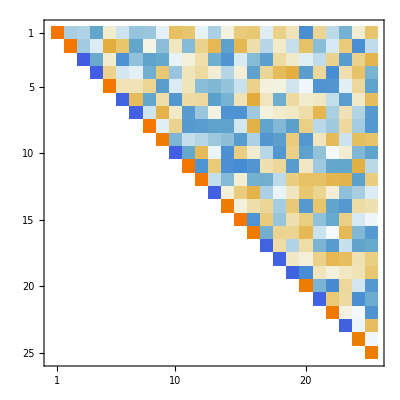

```mathematica
{m,n}={156,25};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A]; Q=Qᵀ;
Map[Dimensions,{A,Q,R}]
Norm[A-Q.R]
Norm[Qᵀ.Q-IdentityMatrix[n]]
MatrixPlot[R]
```

### 6.3 Orthogonal Projections

In calculus you learned how to split a vector y into a piece parallel and perpendicular to another vector u. 
	y_par=(y.u)/(u.u) u
and 
	y_perp=y-(y.u)/(u.u) u

Reminder: A set of vectors {u_1,u_2,…,u_p}in  ℝ^n is orthogonal if u_i.u_j=0 for i≠j.

Reminder: An orthogonal basis for W is an orthogonal set that spans W.

Reminder: A set of vectors {u_1,u_2,…,u_p}in  ℝ^n is orthonormal if u_i.u_j=0 for i≠j and u_i.u_i=1

Reminder: An orthonormal basis for W is an orthonormal set that spans W.

Theorem 8: For an orthogonal basis {u_1,u_2,…,u_p} spanning W⊂ℝ^nand y∈ℝ^n the unique decomposition
	y=ŷ+z
with ŷ∈W and z∈W^⊥ is given by 
	ŷ=(y.u_1)/(u_1.u_1)u_1+(y.u_2)/(u_2.u_2)u_2+…+(y.u_p)/(u_p.u_p)u_p
and z=y-ŷ.

Theorem 8b: For an orthonormal basis {u_1,u_2,…,u_p} spanning W⊂ℝ^nand y∈ℝ^n the unique decomposition
	y=ŷ+z
with ŷ∈W and z∈W^⊥ is given by 
	ŷ=(y.u_1)u_1+(y.u_2)u_2+…+(y.u_p)u_p
and z=y-ŷ.

Definition: ŷ=∑_(i=1)^p (y.u_i)/(u_i.u_i)u_i is the orthogonal projection of y onto the span of the orthogonal basis {u_1,…,u_p}

Theorem 9: Best Approximation
For any subspace W⊂ℝ^n and y∈ℝ^n
	||y-ŷ||< ||y-v|| 
for all v∈ℝ^n with v≠ŷ.

Theorem 10: 
If {u_1,u_2,…,u_p} is an orthonormal basis for W⊂ℝ^n then
	proj_W y=∑_(i=1)^p (y.u_i)u_i=U Uᵀ y
for all y∈ℝ^n

Reminder: A matrix U∈ℝ^(m×n) with orthonormal columns satisfies UᵀU=I_n.

### 6.4 Gram-Schmidt Process

The motto is orthonormal sets are very useful. The question is how to construct an orthonormal basis for a subspace W=span{a_1,a_2,…,a_p}.  The answer is start at the beginning (a very good place to start!) and proceed by induction.

Theorem 11: Gram-Schmidt Process
Given a basis {x_1,x_2,…,x_p} the algorithm below computes an orthonormal basis for span(x_1,x_2,…,x_p).

The motto is “start at the beginning, makes things orthogonal, and then normalize.

3.13154×10^-16

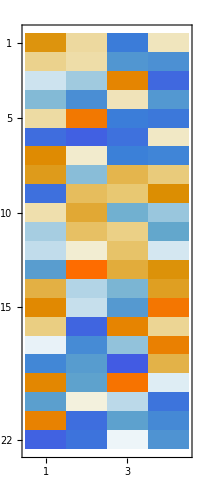

```mathematica
n=22;
{x1,x2,x3,x4}=RandomReal[{-1,1},{4,n}];
(* Fix the length of the first vector *)
u1=x1/Norm[x1];
(* Make the second vector perpendicular to u1 and normalize *)
u2=x2;
u2=u2-(u1.u2)u1;
u2=u2/Norm[u2];
(* Make the third vector perpendicular to u1 and u2 and normalize *)
u3=x3;
u3=u3-(u1.u3)u1;
u3=u3-(u2.u3)u2;
u3=u3/Norm[u3];
(* Make the 4th vector perpendicular to u1 and u2 and u3 and normalize *)
u4=x4;
u4=u4-(u1.u4)u1;
u4=u4-(u2.u4)u2;
u4=u4-(u3.u4)u3;
u4=u4/Norm[u4];
(* Assembling U *)
U = {u1,u2,u3,u4}ᵀ;
Norm[Uᵀ.U-IdentityMatrix[4]]
MatrixPlot[U]
```

I am writing the code slowly!

```mathematica
n=22;
X=RandomReal[{-1,1},{n,4}];
(* Copy X in to U *)
U=X;
(* Fix the first column *)
i=1;
γ=Norm[U⟦All,i⟧];
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Fix the second column *)
i=2;
U⟦All,i⟧=U⟦All,i⟧-(U⟦All,1⟧.U⟦All,i⟧)U⟦All,1⟧;
γ=Norm[U⟦All,i⟧];
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Fix the third column *)
i=3;
U⟦All,i⟧=U⟦All,i⟧-(U⟦All,1⟧.U⟦All,i⟧)U⟦All,1⟧;
U⟦All,i⟧=U⟦All,i⟧-(U⟦All,2⟧.U⟦All,i⟧)U⟦All,2⟧;
γ=Norm[U⟦All,i⟧];
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Fix the 4th column *)
i=4;
U⟦All,i⟧=U⟦All,i⟧-(U⟦All,1⟧.U⟦All,i⟧)U⟦All,1⟧;
U⟦All,i⟧=U⟦All,i⟧-(U⟦All,2⟧.U⟦All,i⟧)U⟦All,2⟧;
U⟦All,i⟧=U⟦All,i⟧-(U⟦All,3⟧.U⟦All,i⟧)U⟦All,3⟧;
γ=Norm[U⟦All,i⟧];
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Check the answwer *)
MatrixForm[Uᵀ.U]
```

(1. | -4.33681×10^-17 | -2.38524×10^-17 | 3.81639×10^-17
-4.33681×10^-17 | 1. | -3.46945×10^-17 | 7.28584×10^-17
-2.38524×10^-17 | -3.46945×10^-17 | 1. | -6.93889×10^-18
3.81639×10^-17 | 7.28584×10^-17 | -6.93889×10^-18 | 1.)

```mathematica
m=22;
n=4;
X=RandomReal[{-1,1},{m,n}];
(* Copy X in to Q *)
U=X;
(* Assign space for R *)
R=ConstantArray[0,{n,n}];
(* Fix the first column *)
i=1;
γ=Norm[U⟦All,i⟧];
R⟦i,i⟧=γ;
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Fix the second column *)
i=2;
α=U⟦All,1⟧.U⟦All,i⟧;
R⟦1,i⟧=α;
U⟦All,i⟧=U⟦All,i⟧-α U⟦All,1⟧;
γ=Norm[U⟦All,i⟧];
R⟦i,i⟧=γ;
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Fix the third column *)
i=3;
α=U⟦All,1⟧.U⟦All,i⟧;
R⟦1,i⟧=α;
U⟦All,i⟧=U⟦All,i⟧-α U⟦All,1⟧;
α=U⟦All,2⟧.U⟦All,i⟧;
R⟦1,i⟧=α;
U⟦All,i⟧=U⟦All,i⟧-α U⟦All,2⟧;
γ=Norm[U⟦All,i⟧];
R⟦i,i⟧=γ;
U⟦All,i⟧=U⟦All,i⟧/γ;
(* Fix the 4th column *)
i=4;

(* Check the answwer *)
TabView[{"UᵀU"->MatrixForm[Uᵀ.U],
"R"->MatrixForm[R]}]
```

12

Theorem 12: QR Factorization 
For A∈ℝ^(m×n) we can factor A=Q R  where Q∈ℝ^(m×n) and R∈ℝ^(n×n) is upper triangular.   The algorithm is below.

Ready to write loops?

```mathematica
{m,n}={22,4};
A=RandomReal[{-1,1},{m,n}];
(* Copy A *)
U=A;
(* Asssign R *)
R=ConstantArray[0,{n,n}];
Do[
Do[
α=R⟦j,i⟧=U⟦All,j⟧.U⟦All,i⟧;
U⟦All,i⟧=U⟦All,i⟧-α U⟦All,j⟧,
{j,1,i-1}];
γ=R⟦i,i⟧=Norm[U⟦All,i⟧];
U⟦All,i⟧=U⟦All,i⟧/γ,
{i,1,n}]
TabView[{"UᵀU"->MatrixForm[Uᵀ.U],
"R"->MatrixForm[R],
"A-U.R"->MatrixPlot[A-U.R,PlotLegends->Automatic]}]
```

123

Ready to write a function?

### 6.5 Least Squares

Definition: For A∈ℝ^(m×n) and b∈ℝ^m a least squares solution  x̂∈ℝ^n of A x=b satisfies
	||b-A x̂||≤||b-A x|| 
for all x∈ℝ^n.  We write
	x̂=argmin_x||b-A x||

If f(x)=x^2-4x+3=(x-2)^2-1 then 
	argmin_x f(x)=2 and min_x f(x)=-1.

Theorem 13: Normal Equations 
Least squares solutions of A x =b solve AᵀA x=Aᵀb.

Theorem 14: For A∈ℝ^(m×n) the following are equivalent
a. A x = b has a unique least squares solution for b∈ℝ^m
b. The columns of A are LI
c. AᵀA∈ℝ^(n×n) is invertible
If true, the least squares solution is x̂=(AᵀA)^-1 Aᵀb

Theorem 15: If the columns of A are LI and A=Q R then
	x̂=R^-1 Qᵀb

Back to our example

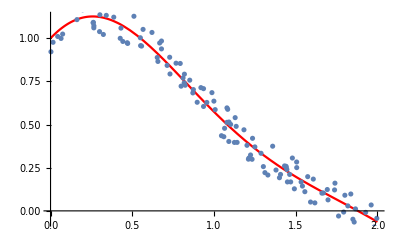

```mathematica
Clear[f,x]
f[x_]:= Sin[x]+Cos[x+ Sin[x]]
ϵ=0.1; SampleSize=123;
AASData=Table[ x=RandomReal[{0,2}];{x, f[x]+ϵ RandomReal[{-1,1}]},{SampleSize}];
Show[
Plot[f[x],{x,0,2},PlotStyle->Red],
ListPlot[AASData]]
```

Lets do a cubic polynomial
	p[x]=a_0+a_1 x + a_2 x^2+a_3 x^3
with four unknowns.  We would like to satisfy
	p[x_i]=y_i
for each of the data points.  There are a lot more data points than unknowns! We can not hit all the data points! What we want is the best cubic polynomial. I want 
	a_0+a_1 x_i+a_2 x_i^2+a_3 x_i^3-y_i≈0
for all the data points.  As a matrix this is 
	V(a_0
a_1
a_2
a_3)-(y_0
y_1
y_2
y_3)≈(0
0
0
0)
where 
	V=(1 | x_1 | x_1^2 | x_1^3
1 | x_2 | x_2^2 | x_2^3
  | ⋮ |   |  
1 | x_s | x_s^2 | x_s^3)∈ℝ^(s×4).  
The best cubic has coefficients minimizing
	||V(a_0
a_1
a_2
a_3)-(y_0
y_1
y_2
y_3)||
Our theorem tells us two recipes to minimize ||A x-b|| where A=Q R
	1) (AᵀA)^-1 Aᵀb
	2) R^-1 Qᵀb 
There are two natural implementations of each recipe. For a tiny problem they are all fast and give identical answers.

```mathematica
A=Table[
x=AASData⟦i,1⟧;
{1,x,x^2,x^3},
{i,1, SampleSize}];
b=Table[
y=AASData⟦i,2⟧;
y,
{i,1, SampleSize}];
{Q,R}=QRDecomposition[A];Q=Qᵀ;
Inverse[Aᵀ.A].Aᵀ.b
LinearSolve[Aᵀ.A,Aᵀ.b]
Inverse[R].Qᵀ.b
{a0,a1,a2,a3}=LinearSolve[R,Qᵀ.b]
```

{1.03086,0.579566,-1.46429,0.460663}

{1.03086,0.579566,-1.46429,0.460663}

{1.03086,0.579566,-1.46429,0.460663}

«1 more identical outputs»

Lets see how well we did!

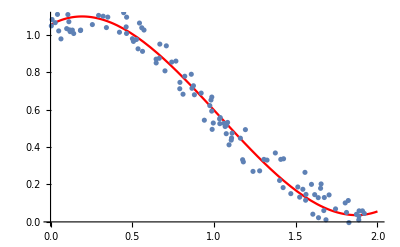

```mathematica
p[x_]:=a0+a1 x + a2 x^2 + a3 x^3
Show[
Plot[p[x],{x,0,2},PlotStyle->Red],
ListPlot[AASData]]
```